# HW 9 - ASTR501 Daniel George - dgeorge5@illinois.edu

#### Q1) Reference: http://iopscience.iop.org/article/10.1086/648121/pdf

```mathematica
Q=Quiet@ToExpression@StringReplace[TextRecognize[-Graphics-,"Line"],{"X"->"*","10-"->"10^-","~"->""}];
Te =Quantity[10000, "Kelvins"];   Evaluate@Array[w,5,0] = {4,6,4,4,2};   ij = Flatten[Table[{i,j},{i,0,4},{j,i+1,4}],1];
Evaluate[λ@@@ij] = Q⟦;;10⟧;    Evaluate[A@@@ij] = Q⟦-10;;⟧; A[0,2] = 1.6 10^-4;
Evaluate[Υ@@@ij] = Q⟦13;;22⟧*{6/10,4/10,4/6,2/6,1,1,1,1,1,1};
Υ[j_,i_]/;j>i = Υ[i,j] Exp[-Quantity[, "PlanckConstant"]Quantity[, "SpeedOfLight"]/(λ[i,j]Quantity[1, "Micrometers"]Quantity[, "BoltzmannConstant"]Te)];    Υ[i_,i_] = 0;
c[i_,j_]=Quantity[, "PlanckConstant"]^2/(2π Quantity[1, "ElectronMass"])^1.5/Sqrt[Quantity[, "BoltzmannConstant"]Te]Quantity[x, 1/("Centimeters")^3]Υ[j,i]/w@i; (* b) Collisional (de)excitation rates *)
f@x_ = First@Solve[Append[Total@Array[n,5,0]==1]@UnitConvert@Table[ (* a) Level population equations *)
 ∑_(j=0)^4 n(j)c(j,i)+∑_(j=i+1)^4 n(j)A(i,j)==∑_(j=0)^4 n(i)c(i,j)+∑_(j=0)^(i-1) n(i)A(j,i),{i,0,4}]/.Quantity[z_,_]:>z,Array[n,5,0]];
```

c) Stimulated emission can be ignored because there are few atoms in higher states which radiatively decay immediately.

```mathematica
Grid[Prepend[Prepend[f[#]⟦;;,2⟧,#]&/@{1,10^4},Prepend["d) n_e"]@Array[n,5,0]],Frame->All]
```

d) n_e | n[0] | n[1] | n[2] | n[3] | n[4]
1 | 0.999988 | 0.0000104704 | 1.57608×10^-6 | 7.56812×10^-11 | 4.91647×10^-11
10000 | 0.969929 | 0.0193661 | 0.0106992 | 4.03822×10^-6 | 1.74191×10^-6

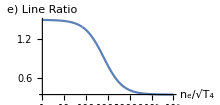

```mathematica
r@ne_:=Divide@@(n@#2A@##/(λ@##)&@@@{{0,1},{0,2}}/.f@ne);  {LogLinearPlot[r@ne,{ne,1,10^6},PlotRange->All,ImageSize->220,AspectRatio->.48,AxesLabel->{"n_e/√T_4","e) Line Ratio"}],#-> r@#&/@{1,10^4}//Column}//GraphicsRow
```

#### Q2 a)

```mathematica
RS=9.77 10^18 (10^48.75/10^49 )^(1/3)Quantity[1, "Centimeters"]//UnitConvert
```

8.0642×10^16 m

#### Q2 b) (Same order as in the question)

```mathematica
UnitConvert[{1.22 10^3 Quantity[1, "Years"],Quantity[5, "Megayears"],2.39 10^5 Quantity[1, "Years"](10^48.75/10^49 )^(1/3)},"Years"]
```

{1220. yr,5000000 yr,197272. yr}

#### Q2 c) Dust is important. Reference: http://www.scielo.org.mx/pdf/rmaa/v51n2/v51n2a10.pdf

```mathematica
nd=NSolve[{(Quantity[100, 1/("Centimeters")^3]Quantity[1.67 10^-24, "Grams"]+nd md).01==nd md,Quantity[3, ("Grams")/("Centimeters")^3]==md/(4/3π Quantity[0.1, "Micrometers"]^3)},{nd,md}]⟦1,1,2⟧;
FindRoot[UnitConvert@((R0/RS)^3==Exp[-(nd π Quantity[0.1, "Micrometers"]^2 R0)])/.Quantity[x_,_]:>x,{R0,10^18}]⟦1,2⟧Quantity[, "Meters"]
```

7.27978×10^16 m